#### Mathematica file to compute New Physics contributions to g-2. Acknowledgments should be referred to: Farinaldo S. Queiroz and William Shepherd [arxiv:1403.2309] and M Lindner, M Platscher, FS Queiroz, https://doi.org/10.1016/j.physrep.2017.12.001 [ arXiv:1610.06587v2]

The reader should straightforwardly use this mathematica file to compute the total contribution of a generic model to the muon magnetic moment at 1-loop level. Plots are also available. We have closely followed the notation of our paper arxiv.

New Physics Contribution to (g-2)_μ

Global Parameters. 
Masses of the SM particles in GeV units.

```mathematica
MN=10; (*Neutral lepton mass MN=(10,100,1000) GeV*)
mμ=0.105; (*Muon mass*)
mν=0.1*10^-9; (*Neutrino mass*)
g=0.65;
SW2=0.231; SW=Sqrt[SW2]; CW=Sqrt[1-SW2]; (*Weinberg angle relations*)
```

Experimental Bounds
based on (old): 

Current Bound: (295 ± 81) x 10^-11; 

Projected Bound:  (295 ± 34) x 10^-11; 

  

based on (new): 

Current Bound: (261 ± 78) x 10^-11; 

Projected Bound:  (261± 34) x 10^-11;

```mathematica
BoundProjectedup=Table[{x,295*10^-11},{x,1,10000,1}];
BoundProjecteddown=Table[{x,227*10^-11},{x,1,10000,1}];
BoundCurrenteup=Table[{x,339*10^-11},{x,1,10000,1}];
BoundCurrentdown=Table[{x,183*10^-11},{x,1,10000,1}];
sigmaCurrent=Table[{x,78*10^-11},{x,1,10000,1}];
sigmaProjected=Table[{x,34*10^-11},{x,1,10000,1}];
```

### Neutral Lepton - K^+ + X^+ . There are two neutral Leptons and two Charged Vectors. I’m assuming them to be degenarate. Hence I multiplied everything by 2.

L ~ g_VK_ρ^+N̄γ^ρμ+g_AX_ρ^+N̄γ^ργ^5μ

```mathematica
ϵ5=MN/mμ; λ5=mμ/MKX; gv5=g/(2*Sqrt[2]); ga5=g/(2*Sqrt[2]);
ΔaNeutralLep=Table[{MKX,2*(-(gv5^2*mμ^2)/(8*π^2*MKX^2)*NIntegrate[(-2*x^2*(1+x-2*ϵ5)+λ5^2*x*(1-x)*(1-ϵ5)^2*(x+ϵ5))/(ϵ5^2*λ5^2*(1-x)*(1-ϵ5^-2*x)+x),{x,0,1}]-(ga5^2*mμ^2)/(8*π^2*MKX^2)*NIntegrate[(-2*x^2*(1+x+2*ϵ5)+λ5^2*x*(1-x)*(1+ϵ5)^2*(x-ϵ5))/(ϵ5^2*λ5^2*(1-x)*(1-ϵ5^-2*x)+x),{x,0,1}])},{MKX,100,10000,10}];
```

```mathematica
(* USe the commands below in case the Neutral Lepton - Higgs mediated contribution of your particular model is negative. This is only necessary
in case the reader is interested in using the ListLogLogPlot below as we did.*)

size5=Dimensions[ΔaNeutralLep];
ΔaNeutralLepnew=Table[{ΔaNeutralLep[[i,1]],-ΔaNeutralLep[[i,2]]},{i,1,size5[[1]]}];

(*Plot of the Neutral Lepton contribution to Subscript[(g-2), μ] as a function of its mass*)
```

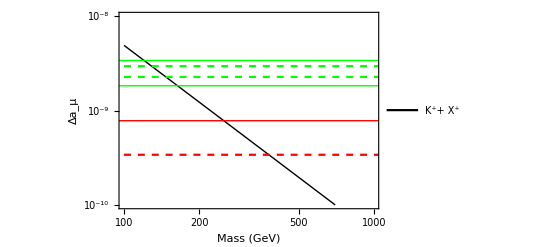

```mathematica
ListLogLogPlot[{ΔaNeutralLep,ΔaNeutralLepnew,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,1000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm["Mass "[GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"K^++ X^+"}],{0.5,0.9}]]
```

#### Z’ boson

L ~ g_v Z'_ρμ̄ γ^ρμ+g_AZ'_ρμ̄γ^ργ^5 μ

```mathematica
mf9=mμ; ϵ9=mf9/mμ;λ9=mμ/MZp;gv9=g/CW*(1-3*SW^2)/(2*√(3*CW^2-1));ga9=g/CW*(-CW^2)/(2*√(3*CW^2-1));
ΔaZp=Table[{MZp,(gv9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2+2*ϵ9)+λ9^2*x^2*(1-ϵ9)^2*(1-x+ϵ9))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] 
+ (ga9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2-2*ϵ9)+λ9^2*x^2*(1+ϵ9)^2*(1-x-ϵ9))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] },{MZp,100,10000,10}];
```

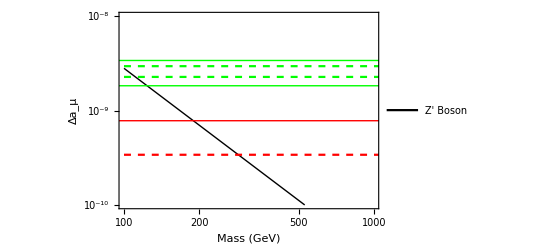

```mathematica
(* USe the commands below in case the Neutral Vector Boson contribution of your particular model is negative. This is only necessary in case the reader is interested in using the ListLogLogPlot below as we did.*)

size9=Dimensions[ΔaZp];
ΔaZpnew=Table[{ΔaZp[[i,1]],-ΔaZp[[i,2]]},{i,1,size9[[1]]}];

(*Plot of the Neutral Vector Boson contribution to Subscript[(g-2), μ] as a function of its mass*)

ListLogLogPlot[{ΔaZpnew,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,1000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm["Mass "[GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"Z' Boson"}],{0.5,0.9}]]
```

COMBINED CONTRIBUTIONS

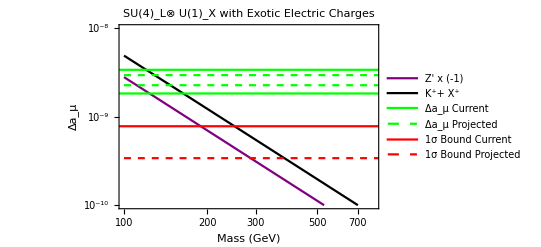

```mathematica
plottotal1=ListLogLogPlot[{ΔaZpnew,ΔaNeutralLep,BoundCurrenteup,BoundProjectedup,sigmaCurrent,sigmaProjected,BoundCurrentdown,BoundProjecteddown},PlotStyle->{Directive[Purple,Thick],Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick],Directive[Green,Dashed]},Joined->True,PlotRange->{{100,800},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm["Mass "[GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"Z' x (-1)","K^++ X^+","Δa_μ Current","Δa_μ Projected","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["SU(4\!\(\*SubscriptBox[\()\), \(L\)]\)⊗ U(1\!\(\*SubscriptBox[\()\), \(X\)]\) with Exotic Electric Charges",12,Black,Bold]]
```

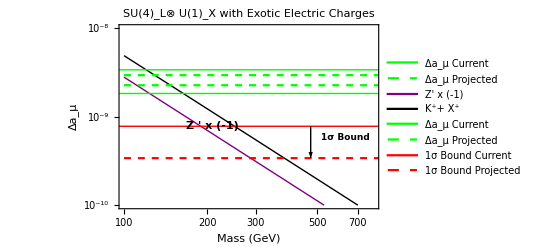

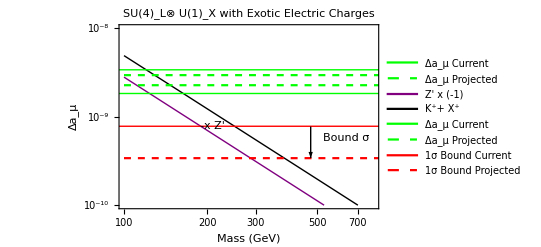

```mathematica
sizetotal=Dimensions[ΔaNeutralLep];
Totalcontri=Table[{ΔaNeutralLep[[i,1]],ΔaNeutralLep[[i,2]]+ΔaZp[[i,2]]},{i,1,sizetotal[[1]]}];
Totalcontrinew=Table[{Totalcontri[[i,1]],-Totalcontri[[i,2]]},{i,1,sizetotal[[1]]}];
plottotal10=ListLogLogPlot[{Totalcontri,BoundCurrenteup,BoundProjectedup,sigmaCurrent,sigmaProjected,BoundCurrentdown,BoundProjecteddown},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick],Directive[Green,Dashed]},Joined->True,PlotRange->{{100,600},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Mass[GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"Total(-1)","\!\(\*SubscriptBox[\(Δa\), \(μ\)]\) Current","\!\(\*SubscriptBox[\(Δa\), \(μ\)]\) Projected","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["SU(4\!\(\*SubscriptBox[\()\), \(L\)]\)⊗ U(1\!\(\*SubscriptBox[\()\), \(X\)]\) with Exotic Electric Charges",12,Black,Bold]]
```